```mathematica
Subscript[Q, sun][t_] = (-0.3416*Cos[t*π/43200]+0.2243*Cos[t*π/(6*3600)]+0.2097)
```

0.2097-0.3416 Cos[(π t)/43200]+0.2243 Cos[(π t)/21600]

```mathematica
Subscript[Q, in][t_] = Subscript[Q, sun][t] * AWindow*1000
```

1000 AWindow (0.2097-0.3416 Cos[(π t)/43200]+0.2243 Cos[(π t)/21600])

```mathematica
(*Subscript[Th, Ab]= 0.2;
Subscript[Density, Ab] = 275;
Subscript[A, absorber]= 16;
Subscript[c, absorber] = 1600;
Subscript[m, absorber] = Subscript[Th, Ab]*Subscript[Density, Ab]*Subscript[A, absorber];
Subscript[m, wall] = 17079.5;
Subscript[c, wall] = .3;
Subscript[c, 1] = Subscript[m, absorber]*Subscript[c, absorber];
Subscript[c, 2] = Subscript[m, wall] * Subscript[c, wall];
Subscript[h, Subscript[air, in]]= 20;
Subscript[h, Subscript[air, out]] = 20;
Subscript[A, wall] = 57.6;
Subscript[k, insulation] = 0.06;
Subscript[L, insulation]= 0.2;
Subscript[T, out] = 270;
Subscript[R, 1] = 1 / (Subscript[h, Subscript[air, in]]*Subscript[A, absorber]);
Subscript[R, 2] = 1 / (Subscript[h, Subscript[air, in]]*Subscript[A, wall]);
Subscript[R, 3] = Subscript[L, insulation] / (Subscript[k, insulation]*Subscript[A, wall]);
Subscript[R, 4] = 1 / (Subscript[h, Subscript[air, out]]*Subscript[A, wall]);
Subscript[c, 1] = Subscript[m, absorber]*Subscript[c, absorber];
Subscript[c, 2] = Subscript[m, wall] * Subscript[c, wall];*)
```

```mathematica
Subscript[Th, Ab]= 2.2;
Subscript[Density, Ab] = 275; (*275 is density of hempcrete and 2168 is density of extrudable concrete*)
Subscript[A, absorber]= 16; (*surface area of the absorber in contact with the sun*)
Subscript[c, absorber] = 1600; (*spec heat of absorber aka hempcrete = 1600 and concrete is 1000*)
Subscript[m, absorber] = Subscript[Th, Ab]*Subscript[Density, Ab]*Subscript[A, absorber];
Subscript[c, wall] = 800; (*spec heat of the wall which is hempcrete = 1600 and concrete is 1000 (not 3d printed concrete, but we couldn't find much)*)
Subscript[c, 1] = Subscript[m, absorber]*Subscript[c, absorber];
Subscript[c, 2] = Subscript[m, wall] * Subscript[c, wall];
Subscript[h, Subscript[air, in]]= 20;
Subscript[h, Subscript[air, out]] = 20;
Subscript[A, wall] = 53;
AWindow = 42/4;
Subscript[Density, insulation]=2168;
Subscript[k, insulation] = 3/10;
Subscript[L, insulation]= 15/100;
Subscript[m, wall] = Subscript[L, insulation]*Subscript[Density, insulation]*Subscript[A, wall];
Subscript[T, out] = 270;
Subscript[R, 1] = 1 / (Subscript[h, Subscript[air, in]]*Subscript[A, absorber]);
Subscript[R, 2] = 1 / (Subscript[h, Subscript[air, in]]*Subscript[A, wall]);
Subscript[R, 3] = Subscript[L, insulation] / (Subscript[k, insulation]*Subscript[A, wall]);
Subscript[R, 4] = 1 / (Subscript[h, Subscript[air, out]]*Subscript[A, wall]);
Subscript[c, 1] = Subscript[m, absorber]*Subscript[c, absorber];
Subscript[c, 2] = Subscript[m, wall] * Subscript[c, wall];
```

```mathematica
Subscript[R, a]:= Subscript[R, 1]+Subscript[R, 2]+Subscript[R, 3]
```

```mathematica
s = NDSolve[{Subscript[T, Ab]'[t] == (Subscript[Q, in][t]-((Subscript[T, Ab][t]-Subscript[T, w][t])/(Subscript[R, a])))/Subscript[c, 1],
Subscript[T, w]'[t] == (((Subscript[T, Ab][t] - Subscript[T, w][t])/(Subscript[R, a]))-((Subscript[T, w][t]-Subscript[T, out])/Subscript[R, 4]))/Subscript[c, 2],
Subscript[T, Ab][0]==293,Subscript[T, w][0]==270},{Subscript[T, Ab],Subscript[T, w]},{t,86400*0,86400*15}]
```

{{T_Ab→InterpolatingFunction[…],T_w→InterpolatingFunction[…]}}

```mathematica
Subscript[T, a][t_] = Subscript[T, w][t] + (Subscript[T, Ab][t] - Subscript[T, w][t])* ((Subscript[R, 2] + Subscript[R, 3])/(Subscript[R, 1]+Subscript[R, 2]+Subscript[R, 3]))/.{%}
```

{{InterpolatingFunction[…][t]+176/229 (-InterpolatingFunction[…][t]+InterpolatingFunction[…][t])}}

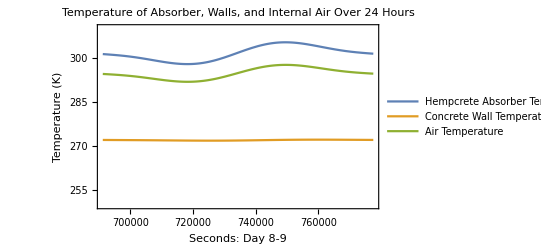

```mathematica
Plot[Evaluate[{Subscript[T, Ab][t],Subscript[T, w][t],Subscript[T, a][t]}/.s],{t,86400*8,86400*9}, PlotRange->{{86400*8, 86400*9},{250, 310}},PlotLabel-> "Temperature of Absorber, Walls, and Internal Air Over 24 Hours",PlotLegends->LineLegend[{"Hempcrete Absorber Temperature", "Concrete Wall Temperature", "Air Temperature"}], Frame->True, FrameLabel->{Style["Seconds: Day 8-9",Black,Small],Style["Temperature (K)",Black,Small]} ]
```

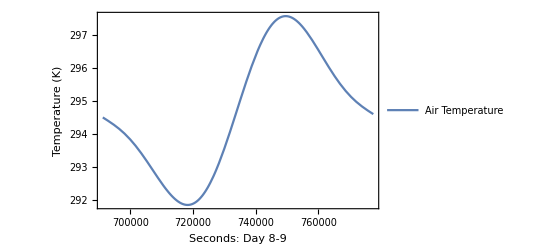

```mathematica
Plot[Evaluate[{Subscript[T, a][t]}/.s],{t,86400*8,86400*9}, PlotLegends->LineLegend[{"Air Temperature"}],Frame->True, FrameLabel->{Style["Seconds: Day 8-9",Black,Small],Style["Temperature (K)",Black,Small]}]
```

```mathematica
min = Subscript[T, a][718000][[1]][[1]]
```

291.841

```mathematica
max = Subscript[T, a][750000][[1]][[1]]
```

297.574

```mathematica
min  = min - 273
max = max -273
```

18.8407

24.5745

### 18.9 - 24.574 degrees celsius

```mathematica
NMaximize[{Subscript[T, a][t],86400*8≤t≤86400*9},t,Method->{"DifferentialEvolution","SearchPoints"->50}]
```

NMaximize::objfs: The objective function {{«1»}} should be scalar-valued.

NMaximize[{{{InterpolatingFunction[…][t]+176/229 (-InterpolatingFunction[…][t]+InterpolatingFunction[…][t])}},691200≤t≤777600},t,Method→{DifferentialEvolution,SearchPoints→50}]

```mathematica
NMaximize[{Subscript[T, a][t],86400*8≤t≤86400*8.5},t,Method->"DifferentialEvolution"]
```

NMaximize::objfs: The objective function {{«1»}} should be scalar-valued.

NMaximize[{{{InterpolatingFunction[…][t]+176/229 (-InterpolatingFunction[…][t]+InterpolatingFunction[…][t])}},691200≤t≤734400.},t,Method→DifferentialEvolution]

```mathematica
Maximize[Subscript[T, a][t], t]
```

Maximize::objfs: The objective function {«1»+176/229 (-InterpolatingFunction[{{«2»}},{5,7,1,{«1»},{«1»},0,0,0,0,Automatic,{},{},False},{{«601»}},{Developer`PackedArrayForm,{«602»},{«1202»}},{Automatic}][t]+«1»)} should be scalar-valued.

Maximize[{{InterpolatingFunction[…][t]+176/229 (-InterpolatingFunction[…][t]+InterpolatingFunction[…][t])}},t]

```mathematica
53*0.15*275
```

2186.25

```mathematica
2168*53*
```

```mathematica
2.6*4
```